#### Lezione 31/01/25

```mathematica
z1 = s {Cos[th1], Sin[th1]}
```

{s Cos[th1],s Sin[th1]}

```mathematica
z3 = r  {Cos[th3],Sin[th3]}
```

{r Cos[th3],r Sin[th3]}

```mathematica
z4 = {d,0}
```

{d,0}

```mathematica
eqpos = z1-z3 -z4
```

{-d+s Cos[th1]-r Cos[th3],s Sin[th1]-r Sin[th3]}

```mathematica
th1sol = ArcTan[(r Sin[th3])/(r Cos[th3]+d)]
```

ArcTan[(r Sin[th3])/(d+r Cos[th3])]

```mathematica
ssol = Flatten[Solve[eqpos[[2]]==0,s]]/.th1->th1sol
```

{s→(d+r Cos[th3]) √(1+(r^2 Sin[th3]^2)/(d+r Cos[th3])^2)}

Solve::ivar: (r (d+rCos[th3]) √(1+rSin[th3]^2/(d+rCos[th3])^2) Sin[th3])/rSin[th3] is not a valid variable.

```mathematica
eqpost = eqpos/.th1->th1[t]/.th3->th3[t]/.s->s[t]
```

{-d-r Cos[th3[t]]+Cos[th1[t]] s[t],s[t] Sin[th1[t]]-r Sin[th3[t]]}

```mathematica
x = th3[t]
```

th3[t]

```mathematica
y = {th1[t], s[t]}
```

{th1[t],s[t]}

```mathematica
eqvel = D[eqpost,t]
```

{Cos[th1[t]] s'[t]-s[t] Sin[th1[t]] th1'[t]+r Sin[th3[t]] th3'[t],Sin[th1[t]] s'[t]+Cos[th1[t]] s[t] th1'[t]-r Cos[th3[t]] th3'[t]}

```mathematica
fx = Flatten[Normal[CoefficientArrays[eqvel, D[x,t]]][[2]]]
```

{r Sin[th3[t]],-r Cos[th3[t]]}

```mathematica
eqvel
```

{Cos[th1[t]] s'[t]-s[t] Sin[th1[t]] th1'[t]+r Sin[th3[t]] th3'[t],Sin[th1[t]] s'[t]+Cos[th1[t]] s[t] th1'[t]-r Cos[th3[t]] th3'[t]}

```mathematica
fy = Normal[CoefficientArrays[eqvel,D[y,t]]][[2]];fy//MatrixForm
```

(-s[t] Sin[th1[t]] | Cos[th1[t]]
Cos[th1[t]] s[t] | Sin[th1[t]])

```mathematica
ydot = -Inverse[fy].fx*D[x,t]//Simplify
```

{(r Cos[th1[t]-th3[t]] th3'[t])/s[t],r Sin[th1[t]-th3[t]] th3'[t]}

```mathematica
th1dot = ydot[[1]]
```

(r Cos[th1[t]-th3[t]] th3'[t])/s[t]

```mathematica
sdot = ydot[[2]]
```

r Sin[th1[t]-th3[t]] th3'[t]

```mathematica
ssdata = {r->0.1, d-> 0.2}
```

{r→0.1,d→0.2}

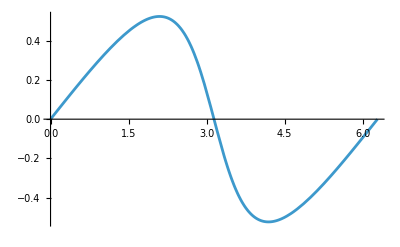

-Graphics-

```mathematica
Plot[th1sol/.ssdata,{th3,0,2Pi}]
```

```mathematica
tauth1th3 = (th1dot/th3'[t])/.th1[t]->th1sol/.s[t]->s/.ssol/.th3[t]->th3
```

(r Cos[th3-ArcTan[(r Sin[th3])/(d+r Cos[th3])]])/((d+r Cos[th3]) √(1+(r^2 Sin[th3]^2)/(d+r Cos[th3])^2))

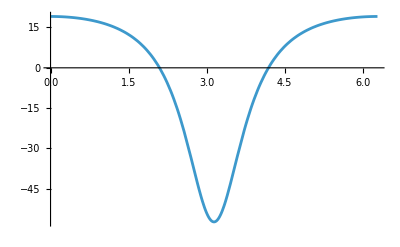

```mathematica
Plot[(180/Pi)tauth1th3/.ssdata,{th3,0,2Pi}]
```

```mathematica
st = s/.ssol
```

(d+r Cos[th3]) √(1+(r^2 Sin[th3]^2)/(d+r Cos[th3])^2)

Part::partw: Part 2 of {{-r Sin[th2[t]] th2'[t]-l Sin[th3[t]] th3'[t]-xB'[t],r Cos[th2[t]] th2'[t]+l Cos[th3[t]] th3'[t]}} does not exist.

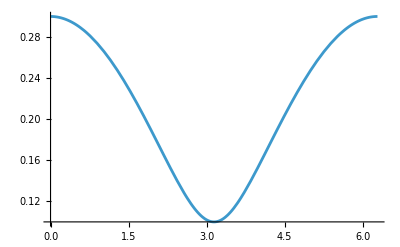

```mathematica
Plot[st/.ssdata,{th3,0,2Pi}]
```